```mathematica
FullSimplify[DSolve[{ x''[t]==(q B)/m y'[t],y''[t]==-(q B)/m x'[t],x[0]==0,x'[0]== 3.1 10^4,y[0]==0,y'[0]== 0},{x[t],y[t]},t]]
```

{{x[t]→(31000. m Sin[(B q t)/m])/(B q),y[t]→(m (-31000.+31000. Cos[(B q t)/m]))/(B q)}}

```mathematica
(31000. m Sin[(B q t)/m])/(B q)/.{m-> 9.1 10^-31, q->1.6 10^-19, B->10^-4}
```

0.00176312 Sin[1.75824×10^7 t]

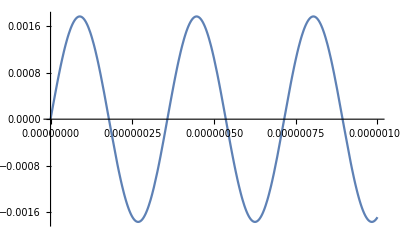

```mathematica
Plot[0.0017631249999999997 Sin[1.7582417582417585*^7 t],{t,0,10^-6}]
```